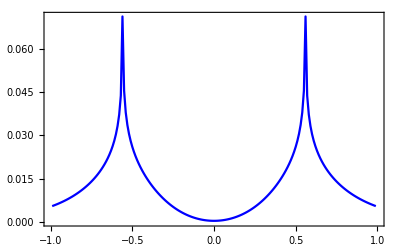

```mathematica
Z1=0;
Z2=0;
Z3=1.58114;
Z4=1.58114;
kF=1;
kFL=1.5Pi;
L=kFL/kF;
ξ=2;
SetSharedVariable[list1]
list1={};
ParallelDo[{
list2={};
Do[{
ϕ=0;
x=-1.6ξ;
x1=0;
η=1;
k=1;
T=0.001;
△=1;
EF=100;
β=1/(k*T);
ω1=(2 N2+1)*π*k*T/△;
fsb=2*Sum[1/(ω1^2+1)^(1/2),{N2,0,300,1}];
ω=(2N1+1)*π*k*T/△;
q=I*ω;
y=(1+p+q/(EF))^(1/2);
y1=(1-p+q/(EF))^(1/2);
y3=(1+p-q/(EF))^(1/2);
y4=(1-p-q/(EF))^(1/2);
yyy=(1+p+q/(EF))^(1/2);
yyy1=(1-p+q/(EF))^(1/2);
yyy3=(1+p-q/(EF))^(1/2);
yyy4=(1-p-q/(EF))^(1/2);
yy=(1+p+q/(EF))^(1/2);
yy1=(1-p+q/(EF))^(1/2);
yy3=(1+p-q/(EF))^(1/2);
yy4=(1-p-q/(EF))^(1/2);
κ=(q^2-1)^(1/2)*kF/(2*EF);
keS=kF+κ;
khS=kF-κ;
kES=(1+(q^2-1)^(1/2)/EF)^(1/2);
kHS=(1-(q^2-1)^(1/2)/EF)^(1/2);
u=(1/2*(1+((q^2-1)^(1/2))/(q)))^(1/2);
v=(1/2*(1-((q^2-1)^(1/2))/(q)))^(1/2);
G[ϕ_]:=({{u, 0, 0, v, -1/2^(1/2), -1/2^(1/2)*E^((I kFL*y)/2), 1/2^(1/2), 1/2^(1/2)*E^((I kFL*y1)/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -u, -v, 0, -1/2^(1/2), -1/2^(1/2)*E^((I kFL*y)/2), -1/2^(1/2), -1/2^(1/2)*E^((I kFL*y1)/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, v, u, 0, 0, 0, 0, 0, -1/2^(1/2), -1/2^(1/2)*E^(-(I kFL*y3)/2), 1/2^(1/2), 1/2^(1/2)*E^(-(I kFL*y4)/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {v, 0, 0, u, 0, 0, 0, 0, -1/2^(1/2), -1/2^(1/2)*E^(-(I kFL*y3)/2), -1/2^(1/2), -1/2^(1/2)*E^(-(I kFL*y4)/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {u*kES, 0, 0, -v*kHS, (y+2*I*Z1)/2^(1/2), -(y-2*I*Z1)/2^(1/2)*E^((I kFL*y)/2), -(y1+2*I*Z1)/2^(1/2), (y1-2*I*Z1)/2^(1/2)*E^((I kFL*y1)/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -u*kES, v*kHS, 0, (y+2*I*Z1)/2^(1/2), -(y-2*I*Z1)/2^(1/2)*E^((I kFL*y)/2), (y1+2*I*Z1)/2^(1/2), -(y1-2*I*Z1)/2^(1/2)*E^((I kFL*y1)/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, v*kES, -u*kHS, 0, 0, 0, 0, 0, -(y3-2*I*Z1)/2^(1/2), (y3+2*I*Z1)/2^(1/2)*E^(-(I kFL*y3)/2), (y4-2*I*Z1)/2^(1/2), -(y4+2*I*Z1)/2^(1/2)*E^(-(I kFL*y4)/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {v*kES, 0, 0, -u*kHS, 0, 0, 0, 0, -(y3-2*I*Z1)/2^(1/2), (y3+2*I*Z1)/2^(1/2)*E^(-(I kFL*y3)/2), -(y4-2*I*Z1)/2^(1/2), (y4+2*I*Z1)/2^(1/2)*E^(-(I kFL*y4)/2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/2^(1/2)*E^((I kFL*y)/2), 1/2^(1/2), -1/2^(1/2)*E^((I kFL*y1)/2), -1/2^(1/2), 0, 0, 0, 0, -1/2^(1/2), -1/2^(1/2)*E^((I kFL*yyy)/4), -I/2^(1/2), -I/2^(1/2)*E^((I kFL*yyy1)/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/2^(1/2)*E^((I kFL*y)/2), 1/2^(1/2), 1/2^(1/2)*E^((I kFL*y1)/2), 1/2^(1/2), 0, 0, 0, 0, -I/2^(1/2), -I/2^(1/2)*E^((I kFL*yyy)/4), -1/2^(1/2), -1/2^(1/2)*E^((I kFL*yyy1)/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1/2^(1/2)*E^(-(I kFL*y3)/2), 1/2^(1/2), -1/2^(1/2)*E^(-(I kFL*y4)/2), -1/2^(1/2), 0, 0, 0, 0, -1/2^(1/2), -1/2^(1/2)*E^(-(I kFL*yyy3)/4), I/2^(1/2), I/2^(1/2)*E^(-(I kFL*yyy4)/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1/2^(1/2)*E^(-(I kFL*y3)/2), 1/2^(1/2), 1/2^(1/2)*E^(-(I kFL*y4)/2), 1/2^(1/2), 0, 0, 0, 0, I/2^(1/2), I/2^(1/2)*E^(-(I kFL*yyy3)/4), -1/2^(1/2), -1/2^(1/2)*E^(-(I kFL*yyy4)/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (y-2*I*Z3)*E^((I kFL*y)/2), -(y+2*I*Z3), -(y1-2*I*Z3)*E^((I kFL*y1)/2), (y1+2*I*Z3), 0, 0, 0, 0, -yyy, yyy*E^((I kFL*yyy)/4), -I*yyy1, I*yyy1*E^((I kFL*yyy1)/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (y-2*I*Z3)*E^((I kFL*y)/2), -(y+2*I*Z3), (y1-2*I*Z3)*E^((I kFL*y1)/2), -(y1+2*I*Z3), 0, 0, 0, 0, -I*yyy, I*yyy*E^((I kFL*yyy)/4), -yyy1, yyy1*E^((I kFL*yyy1)/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -(y3+2*I*Z3)*E^(-(I kFL*y3)/2), (y3-2*I*Z3), (y4+2*I*Z3)*E^(-(I kFL*y4)/2), -(y4-2*I*Z3), 0, 0, 0, 0, yyy3, -yyy3*E^(-(I kFL*yyy3)/4), -I*yyy4, I*yyy4*E^(-(I kFL*yyy4)/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -(y3+2*I*Z3)*E^(-(I kFL*y3)/2), (y3-2*I*Z3), -(y4+2*I*Z3)*E^(-(I kFL*y4)/2), (y4-2*I*Z3), 0, 0, 0, 0, -I*yyy3, I*yyy3*E^(-(I kFL*yyy3)/4), yyy4, -yyy4*E^(-(I kFL*yyy4)/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2^(1/2)*E^((I kFL*yyy)/4), 1/2^(1/2), I/2^(1/2)*E^((I kFL*yyy1)/4), I/2^(1/2), 0, 0, 0, 0, -1, -E^((I kFL*yy)/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, I/2^(1/2)*E^((I kFL*yyy)/4), I/2^(1/2), 1/2^(1/2)*E^((I kFL*yyy1)/4), 1/2^(1/2), 0, 0, 0, 0, 0, 0, -1, -E^((I kFL*yy1)/4), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2^(1/2)*E^(-(I kFL*yyy3)/4), 1/2^(1/2), -I/2^(1/2)*E^(-(I kFL*yyy4)/4), -I/2^(1/2), 0, 0, 0, 0, -1, -E^(-(I kFL*yy3)/4), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -I/2^(1/2)*E^(-(I kFL*yyy3)/4), -I/2^(1/2), 1/2^(1/2)*E^(-(I kFL*yyy4)/4), 1/2^(1/2), 0, 0, 0, 0, 0, 0, -1, -E^(-(I kFL*yy4)/4), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (yyy-2*I*Z4)/2^(1/2)*E^((I kFL*yyy)/4), -(yyy+2*I*Z4)/2^(1/2), (I*(yyy1-2*I*Z4))/2^(1/2)*E^((I kFL*yyy1)/4), -(I*(yyy1+2*I*Z4))/2^(1/2), 0, 0, 0, 0, -yy, yy*E^((I kFL*yy)/4), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (I*(yyy-2*I*Z4))/2^(1/2)*E^((I kFL*yyy)/4), -(I*(yyy+2*I*Z4))/2^(1/2), (yyy1-2*I*Z4)/2^(1/2)*E^((I kFL*yyy1)/4), -(yyy1+2*I*Z4)/2^(1/2), 0, 0, 0, 0, 0, 0, -yy1, yy1*E^((I kFL*yy1)/4), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(yyy3+2*I*Z4)/2^(1/2)*E^(-(I kFL*yyy3)/4), (yyy3-2*I*Z4)/2^(1/2), (I*(yyy4+2*I*Z4))/2^(1/2)*E^(-(I kFL*yyy4)/4), -(I*(yyy4-2*I*Z4))/2^(1/2), 0, 0, 0, 0, yy3, -yy3*E^(-(I kFL*yy3)/4), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (I*(yyy3+2*I*Z4))/2^(1/2)*E^(-(I kFL*yyy3)/4), -(I*(yyy3-2*I*Z4))/2^(1/2), -(yyy4+2*I*Z4)/2^(1/2)*E^(-(I kFL*yyy4)/4), (yyy4-2*I*Z4)/2^(1/2), 0, 0, 0, 0, 0, 0, yy4, -yy4*E^(-(I kFL*yy4)/4), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, E^((I kFL*yy)/4), 1, 0, 0, 0, 0, 0, 0, -u*Exp[I*ϕ], 0, 0, -v*Exp[I*ϕ]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, E^((I kFL*yy1)/4), 1, 0, 0, 0, 0, 0, u*Exp[I*ϕ], v*Exp[I*ϕ], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, E^(-(I kFL*yy3)/4), 1, 0, 0, 0, -v, -u, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, E^(-(I kFL*yy4)/4), 1, -v, 0, 0, -u}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (yy-2 I Z2)*E^((I kFL*yy)/4), -(yy+2 I Z2), 0, 0, 0, 0, 0, 0, -u*kES*Exp[I*ϕ], 0, 0, v*kHS*Exp[I*ϕ]}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (yy1-2 I Z2)*E^((I kFL*yy1)/4), -(yy1+2 I Z2), 0, 0, 0, 0, 0, u*kES*Exp[I*ϕ], -v*kHS*Exp[I*ϕ], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(yy3+2 I Z2)*E^(-(I kFL*yy3)/4), (yy3-2 I Z2), 0, 0, 0, -v*kES, u*kHS, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(yy4+2 I Z2)*E^(-(I kFL*yy4)/4), (yy4-2 I Z2), -v*kES, 0, 0, u*kHS}});
H=({{-u}, {0}, {0}, {-v}, {u*kES}, {0}, {0}, {v*kES}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
H3=({{-v}, {0}, {0}, {-u}, {-v*kHS}, {0}, {0}, {-u*kHS}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
H1=({{0}, {u}, {-v}, {0}, {0}, {-u*kES}, {v*kES}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
H2=({{0}, {v}, {-u}, {0}, {0}, {v*kHS}, {-u*kHS}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
Sol[ϕ_]:=LinearSolve[G[ϕ],H];
Sol3[ϕ_]:=LinearSolve[G[ϕ],H3];
Sol1[ϕ_]:=LinearSolve[G[ϕ],H1];
Sol2[ϕ_]:=LinearSolve[G[ϕ],H2];
b11=Sol[ϕ][[1,1]];
b12=Sol[ϕ][[2,1]];
a11=(kHS/kES)^(1/2)*Sol[ϕ][[3,1]];
a12=(kHS/kES)^(1/2)*Sol[ϕ][[4,1]];
b21=Sol1[ϕ][[1,1]];
b22=Sol1[ϕ][[2,1]];
a21=(kHS/kES)^(1/2)*Sol1[ϕ][[3,1]];
a22=(kHS/kES)^(1/2)*Sol1[ϕ][[4,1]];
b31=(kES/kHS)^(1/2)*Sol2[ϕ][[1,1]];
b32=(kES/kHS)^(1/2)*Sol2[ϕ][[2,1]];
a31=Sol2[ϕ][[3,1]];
a32=Sol2[ϕ][[4,1]];
b41=(kES/kHS)^(1/2)*Sol3[ϕ][[1,1]];
b42=(kES/kHS)^(1/2)*Sol3[ϕ][[2,1]];
a41=Sol3[ϕ][[3,1]];
a42=Sol3[ϕ][[4,1]];
f0O=1/(8 keS khS (u-v) (u+v))ⅈ ⅇ^(-ⅈ (keS+khS) (L+x+x1)) (b32 ⅇ^(1/2 ⅈ (keS L+3 khS L+2 khS (x+x1))) (ⅇ^(ⅈ (keS+khS) x)-ⅇ^(ⅈ (keS+khS) x1)) keS u^2+b41 ⅇ^(1/2 ⅈ (keS L+3 khS L+2 khS (x+x1))) (ⅇ^(ⅈ (keS+khS) x)-ⅇ^(ⅈ (keS+khS) x1)) keS u^2+v (-(a12+a21) ⅇ^(1/2 ⅈ (keS L+3 khS L+2 keS x+4 khS x+2 khS x1)) khS v+(a12+a21) ⅇ^(1/2 ⅈ (keS L+3 khS L+2 khS x+2 keS x1+4 khS x1)) khS v)) η;
f11O=-1/(4 keS khS (u^2-v^2))ⅈ ⅇ^(-ⅈ keS (L+x+x1))(b31 (ⅇ^(1/2 ⅈ (keS+khS) (L+2 x))+ⅇ^(1/2 ⅈ (keS+khS) (L+2 x1))) keS u^2+2 a32 ⅇ^(ⅈ (keS+khS) (L+x+x1)) keS u v+khS v (2 b21 u+a22 (ⅇ^(1/2 ⅈ (keS+khS) (L+2 x))+ⅇ^(1/2 ⅈ (keS+khS) (L+2 x1))) v)) η;
f22O=1/(4 keS khS (u^2-v^2))ⅈ ⅇ^(-ⅈ keS (L+x+x1)) (b42 (ⅇ^(1/2 ⅈ (keS+khS) (L+2 x))+ⅇ^(1/2 ⅈ (keS+khS) (L+2 x1))) keS u^2+2 a41 ⅇ^(ⅈ (keS+khS) (L+x+x1)) keS u v+khS v (2 b12 u+a11 (ⅇ^(1/2 ⅈ (keS+khS) (L+2 x))+ⅇ^(1/2 ⅈ (keS+khS) (L+2 x1))) v)) η;
f3O=1/(8 keS khS (u-v) (u+v))ⅈ ⅇ^(-ⅈ keS (L+x+x1)) (b32 (ⅇ^(1/2 ⅈ (keS+khS) (L+2 x))+ⅇ^(1/2 ⅈ (keS+khS) (L+2 x1))) keS u^2-b41(ⅇ^(1/2 ⅈ (keS+khS) (L+2 x))+ⅇ^(1/2 ⅈ (keS+khS) (L+2 x1))) keS u^2+v (2 a31 ⅇ^(ⅈ (keS+khS) (L+x+x1)) keS u-2 a42 ⅇ^(ⅈ (keS+khS) (L+x+x1)) keS u-khS (2 b11 u-2 b22 u+(a12-a21) (ⅇ^(1/2 ⅈ (keS+khS) (L+2 x))+ⅇ^(1/2 ⅈ (keS+khS) (L+2 x1))) v))) η;
f0E=-1/(8 keS khS (u^2-v^2))ⅈ ⅇ^(-ⅈ (keS+khS) (L+x+x1)) (b32 ⅇ^(1/2 ⅈ (keS L+3 khS L+2 khS (x+x1))) (ⅇ^(ⅈ (keS+khS) x)+ⅇ^(ⅈ (keS+khS) x1)) keS u^2+b41 ⅇ^(1/2 ⅈ (keS L+3 khS L+2 khS (x+x1))) (ⅇ^(ⅈ (keS+khS) x)+ⅇ^(ⅈ (keS+khS) x1)) keS u^2+v (2 a31 ⅇ^(ⅈ (keS+2 khS) (L+x+x1)) keS u+2 a42 ⅇ^(ⅈ (keS+2 khS) (L+x+x1)) keS u+4 ⅇ^(ⅈ (khS (L+2 x)+keS (L+x+x1))) keS u+2 b11 ⅇ^(ⅈ khS (L+x+x1)) khS u+2 b22 ⅇ^(ⅈ khS (L+x+x1)) khS u+4 ⅇ^(ⅈ (khS (L+x+x1)+keS (L+2 x1))) khS u+a12 ⅇ^(1/2 ⅈ (keS L+3 khS L+2 keS x+4 khS x+2 khS x1)) khS v+a21 ⅇ^(1/2 ⅈ (keS L+3 khS L+2 keS x+4 khS x+2 khS x1)) khS v+a12 ⅇ^(1/2 ⅈ (keS L+3 khS L+2 khS x+2 keS x1+4 khS x1)) khS v+a21 ⅇ^(1/2 ⅈ (keS L+3 khS L+2 khS x+2 keS x1+4 khS x1)) khS v)) η;
f11E=(ⅈ ⅇ^(-ⅈ keS (L+x+x1)) (ⅇ^(1/2 ⅈ (keS+khS) (L+2 x))-ⅇ^(1/2 ⅈ (keS+khS) (L+2 x1))) (b31 keS u^2-a22 khS v^2) η)/(4 keS khS (u^2-v^2));
f22E=(ⅈ ⅇ^(-ⅈ keS (L+x+x1)) (-ⅇ^(1/2 ⅈ (keS+khS) (L+2 x))+ⅇ^(1/2 ⅈ (keS+khS) (L+2 x1))) (b42 keS u^2-a11 khS v^2) η)/(4 keS khS (u^2-v^2));
f3E=-(ⅈ ⅇ^(-ⅈ keS (L+x+x1)) (ⅇ^(1/2 ⅈ (keS+khS) (L+2 x))-ⅇ^(1/2 ⅈ (keS+khS) (L+2 x1))) ((b32-b41) keS u^2+(a12-a21) khS v^2) η)/(8 keS khS (u-v) (u+v));
list2=AppendTo[list2,f0O/fsb]},{N1,0,300,1}];
list2=Sort[list2];
list1p=Total[list2];
list1pp=AppendTo[list1,{p,list1p}]},{p,-0.99,0.99,0.01}];
list1pp=Sort[list1];
list1ppp=list1pp/.{xx_,yy_}->{xx,Abs[yy]};
<<MaTeX`
ListLinePlot[list1ppp,FrameLabel->(MaTeX[#,Magnification->25/12]&)/@{"m/E_F","|f_{0}^{O}/f_{sb}|"},AxesOrigin->{0,0},PlotRange->{{-1,1},{0,All}},TicksStyle->Directive[Black],BaseStyle->{FontFamily->"Times",FontSize->15},AxesStyle->{Thickness[0.002],Thickness[0.002]},LabelStyle->Directive[Black],PlotStyle->{{Blue},{Red},{Black}},Frame->True,PlotRangePadding->0,FrameStyle->Directive[Black],Axes->False]
```